```mathematica
u={u1,u2}
L={{-5,1},{5,-1}};
T=Eigenvectors[L];
FindInstance[u.T.{{-6,0},{0,0}}.Inverse[T].u>0&&u1≥0&&u2≥0&&u1+u2==1,u]
Reduce[u.L.u≤0,u]
```

{u1,u2}

{{u1→1/4,u2→3/4}}

u2∈ℝ&&((u1<0&&(u2≤5 u1||u2≥u1))||u1==0||(u1>0&&(u2≤u1||u2≥5 u1)))

{-5,5}

{-5 (1-5 dt)+5 dt,5 (1-5 dt)-5 dt}

{(5 dt)/4+1/4 (5 (1-5 dt)-5 dt) dt-5 (1-(5 dt)/4+1/4 dt (-5 (1-5 dt)+5 dt)),-(5 dt)/4-1/4 (5 (1-5 dt)-5 dt) dt+5 (1-(5 dt)/4+1/4 dt (-5 (1-5 dt)+5 dt))}

{{dt→Root0.309Root[-1+5 #1-15 #1^2+30 #1^3&,1]0.30948645711516276}}

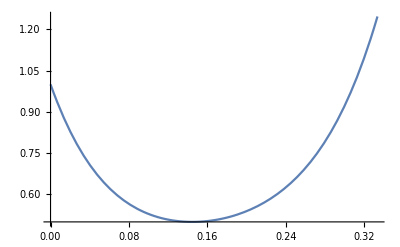

```mathematica
ClearAll["Global`*"]
(*dt=3/10;*)
L={{-5,1},{5,-1}};
u0={1,0};
y1=u0;
y2=u0+dt*L.y1;
y3=u0+1/4*dt*L.y1+1/4*dt*L.y2;
u1=Simplify[u0+1/6*dt*L.y1+1/6*dt*L.y2+2/3*dt*L.y3];

L.y1
L.y2
L.y3

Solve[u1[[1]]^2+u1[[2]]^2==1&&dt>0,dt]
Plot[u1[[1]]^2+u1[[2]]^2,{dt,0,1/3}]
```